```mathematica
CZangle[M_] := (
z = (M[[4, 4]]*M[[1, 1]])/(M[[2, 2]]*M[[3, 3]]);
ArcTan[Re[z], Im[z]]
)
Zangle[M_] := (
z = M[[2, 2]]/M[[1, 1]];
ArcTan[Re[z], Im[z]]
)
```

```mathematica
setVariables[]

Tmax = 2*10^-6;

ΔE = 2000;

Eamp[t_] := 30*cosWindow[t, Tmax/2, Tmax];
ωE = 2*π*(ϵ0 + A/4 - A*dState[[1]]^2) + 2*π*30*10^6;

(* turn off oscillatin' magnetic field *)
Bamp[t_] := 0
ωB = (ωB + ωE)/2;

(*Hdip[[33, 33]] - Hdip[[1, 1]]
Hdip[[37, 37]] - Hdip[[5, 5]]

HcorrectedStatic[[5, 5]] - HcorrectedStatic[[1, 1]]
HcorrectedStatic[[6, 6]] - HcorrectedStatic[[2, 2]]

(H2[[33, 33]] - H2[[1, 1]]) /. t->0
(H2[[37, 37]] - H2[[5, 5]]) /. t->0*)

U = findEvolutionOperator4D[H2];

clearVariables[]
```

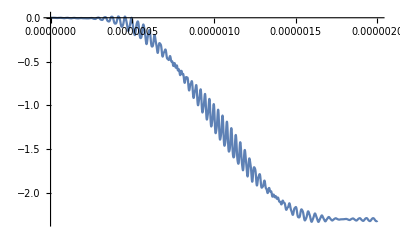

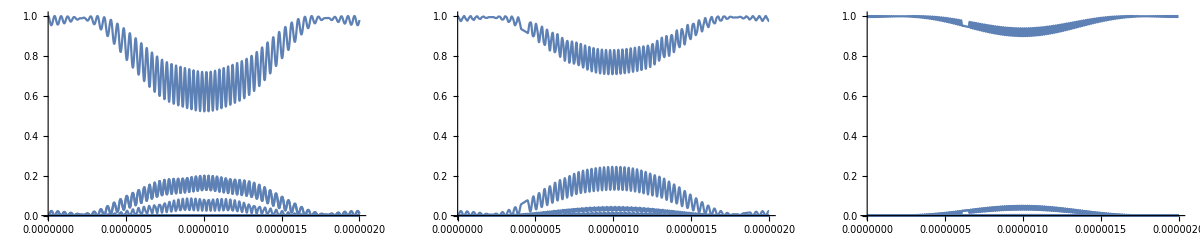

(0.979934 | 0. | 0. | 0.
0. | 0.974409 | 0. | 0.
0. | 7.03648×10^-8 | 0. | 0.
0.00968384 | 0. | 0. | 0.
0. | 0.00275915 | 0. | 0.
0. | 0. | 0.974409 | 0.
0. | 0. | 0. | 0.994719
0. | 0. | 0. | 6.87777×10^-8
0. | 0. | 0.0226994 | 0.
0. | 0. | 0. | 0.00269043
0. | 0. | 7.03648×10^-8 | 0.
0. | 0. | 0. | 6.87777×10^-8
0. | 0. | 0. | 1.18043×10^-14
0. | 0. | 3.40466×10^-9 | 0.
0. | 0. | 0. | 4.51037×10^-10
0.00968384 | 0. | 0. | 0.
0. | 0.0226994 | 0. | 0.
0. | 3.40466×10^-9 | 0. | 0.
0.00069871 | 0. | 0. | 0.
0. | 0.000132911 | 0. | 0.
0. | 0. | 0.00275915 | 0.
0. | 0. | 0. | 0.00269043
0. | 0. | 0. | 4.51037×10^-10
0. | 0. | 0.000132911 | 0.
0. | 0. | 0. | 0.0000169925)

```mathematica
Tmax = 2*10^-6;

Plot[CZangle[U], {t, 0, Tmax}]

GraphicsGrid[{{Plot[Abs[Uuncut[[All, 1]]]^2, {t, 0, Tmax}, PlotRange->All], Plot[Abs[Uuncut[[All, 2]]]^2, {t, 0, Tmax}, PlotRange->All], Plot[Abs[Uuncut[[All, 4]]]^2, {t, 0, Tmax}, PlotRange->All]}}, ImageSize->Full]

Abs[Uuncut /. t->Tmax]^2 // MatrixForm
```

{1.23961,0.880673,-0.0000465595}

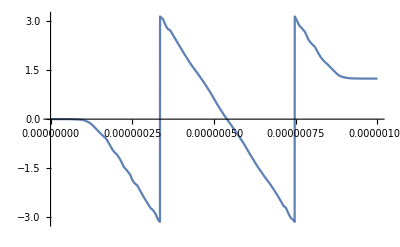

$Aborted

(0.999968 | 0. | 0. | 0.
0. | 1.00006 | 0. | 0.
0. | 1.1556×10^-9 | 0. | 0.
0.0000444457 | 0. | 0. | 0.
0. | 6.85514×10^-7 | 0. | 0.
0. | 0. | 1.00006 | 0.
0. | 0. | 0. | 1.0001
0. | 0. | 0. | 9.61731×10^-9
0. | 0. | 0.0000234588 | 0.
0. | 0. | 0. | 1.29497×10^-7
0. | 0. | 1.1556×10^-9 | 0.
0. | 0. | 0. | 9.61731×10^-9
0. | 0. | 0. | 2.46655×10^-16
0. | 0. | 3.35247×10^-14 | 0.
0. | 0. | 0. | 9.51286×10^-16
0.0000444457 | 0. | 0. | 0.
0. | 0.0000234588 | 0. | 0.
0. | 3.35247×10^-14 | 0. | 0.
4.65623×10^-6 | 0. | 0. | 0.
0. | 2.32559×10^-10 | 0. | 0.
0. | 0. | 6.85514×10^-7 | 0.
0. | 0. | 0. | 1.29497×10^-7
0. | 0. | 0. | 9.51286×10^-16
0. | 0. | 2.32559×10^-10 | 0.
0. | 0. | 0. | 5.58403×10^-11)

```mathematica
setVariables[]

dDip = 500*10^-9;

T1 = 5*10^-9;
Tmax = 1000*10^-9;
T2 = Tmax - 2*T1;

Clear[ΔE];

Ea = 40*Min[1, T2/(300*10^-9)];
T3 = Min[T2/2, 300*10^-9];
Eamp[t_] := Ea*cosWindow[t - T1, T3, T2]
ωE = 2*π*(ϵ0 + A/4 - A*dState[[1]]^2/2) - 2*π*10*10^6 /. ΔE->2000;

(* turn off oscillatin' magnetic field *)
Bamp[t_] := 0
ωB = (ωB + ωE)/2;

(*ΔE = 2000;*)
ΔE = 10000 - 8000*twoPointWindow[t, T1, Tmax, 1];

(*ωE - (H2[[5, 5]] - H2[[1, 1]]) /. t->Tmax/2
ωE - (H2[[37, 37]] - H2[[33, 33]]) /. t->Tmax/2

ωE - (H2[[6, 6]] - H2[[2, 2]]) /. t->Tmax/2
ωE - (H2[[38, 38]] - H2[[34, 34]]) /. t->Tmax/2*)

(*statesInEnergyOrder[Hcorrected] // MatrixForm
Chop[statesInEnergyOrder[H2], 10^-5] // MatrixForm*)

Ubase = MatrixExp[-ⅈ*t*(H2[[{1, 2, 9, 10}, {1, 2, 9, 10}]] /. t->0)];

(*U = findEvolutionOperator4D[H2];*)
(*Utheory = MatrixExp[-ⅈ*H2*t][[{1, 2, 9, 10}, {1, 2, 9, 10}]];*)

(*Chop[statesInEnergyOrder[H2], 10^-5] // MatrixForm*)

Ufinal = ConjugateTranspose[Ubase].U /. t->Tmax;
ϕ = CZangle[Ufinal];
ϕz = -Zangle[Ufinal];

pNonAd = 1 - Sum[Abs[Ufinal[[i, i]]]^2, {i, 4}]/4;

{ϕ, ϕz, pNonAd}

(*TProduct[MatrixExp[-ⅈ*ϕz*σZ/2], MatrixExp[-ⅈ*ϕz*σZ/2]].Ufinal // MatrixForm

Ufinal // CZangle
TProduct[MatrixExp[-ⅈ*ϕz*σZ/2], MatrixExp[-ⅈ*ϕz*σZ/2]].Ufinal // CZangle*)

Plot[CZangle[U], {t, 0, Tmax}]

GraphicsGrid[{{Plot[Abs[Uuncut[[All, 1]]]^2, {t, 0, Tmax}, PlotRange->All], Plot[Abs[Uuncut[[All, 2]]]^2, {t, 0, Tmax}, PlotRange->All], Plot[Abs[Uuncut[[All, 4]]]^2, {t, 0, Tmax}, PlotRange->All]}}, ImageSize->Full]

Abs[Uuncut /. t->Tmax]^2 // MatrixForm


clearVariables[]
```